# Mosquito population dynamics include Early instars, layter instars, pupae, and adults female.

## How to use

Using the code here we can determine seasonal patterns in infection and test the effect of IRS on the mosquito populations. This is a deterministic implementation of the model by White et al. 2011, which itself relies on other references and particularly Griffin et al. 2010. The workflow is to feed the function here the seasonal and or IRS scheme that we want and to take the output and feed it to the parameter file of the ABM. The final vector should be normalized by the predicted abundance without an intervention, to get the amplitude to multiply the biting rate parameter in the model.

White MT, Griffin JT, Churcher TS, Ferguson NM, Basáñez M-G, Ghani AC. Modelling the impact of vector control interventions on Anopheles gambiae population dynamics. Parasit Vectors. 2011;4: 153.

```mathematica
ClearAll[A,P,L,M,K,f,MuM,MuE,MuL, c, TimeMax];
```

## Carrying capacity

```mathematica
Seasonality 1  (not sure what the values here were!)
```

```mathematica
(*Typically the values would be FirstDayOfRain=160 & LastDayOfRain=270. For the PLOS Biol paper use FirstDayOfRain=145.*)
FirstDayOfRain=160 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(0.5+0.5*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0,45 and the addition of 0.55 is to define a minimum (positive) and a maximum value for the number of mosquitos. *) (* Carrying capacity is just a sin function (this is not from the paper). The width (frequency) is matched to the length of the rainy season. the 10000 is just an arbitrary number. Carrying capacity is just for the first 2 stages (denoted "A" in the ODE model below), as their mortality rates depend on carrying capacity *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},100];  (*Seasonality in carrying capacity. Here, we mimic the Bongo-District seasonality pattern with a short wet season between Jun-Oct (days 180-300) and a prolonged
dry season between Nov-May (days 0-179 and 301-360). In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
Seasonality 2 (not sure what the values here were!)
```

```mathematica
(*Typically the values would be FirstDayOfRain=160 & LastDayOfRain=270. For the PLOS Biol paper use FirstDayOfRain=145.*)
FirstDayOfRain=145 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(0.55+0.45*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0,45 and the addition of 0.55 is to define a minimum (positive) and a maximum value for the number of mosquitos. *) (* Carrying capacity is just a sin function (this is not from the paper). The width (frequency) is matched to the length of the rainy season. the 10000 is just an arbitrary number. Carrying capacity is just for the first 2 stages (denoted "A" in the ODE model below), as their mortality rates depend on carrying capacity *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},1000];  (*Seasonality in carrying capacity. Here, we mimic the Bongo-District seasonality pattern with a short wet season between Jun-Oct (days 180-300) and a prolonged
dry season between Nov-May (days 0-179 and 301-360). In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
Seasonality 3
```

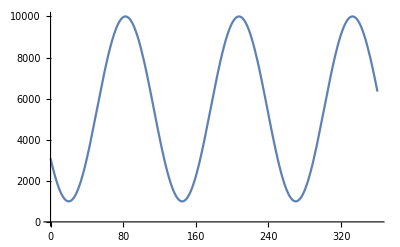

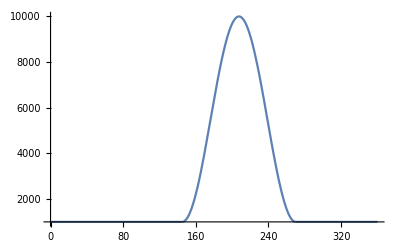

```mathematica
(*Typically the values would be FirstDayOfRain=160 & LastDayOfRain=270. For the PLOS Biol paper use FirstDayOfRain=145.*)
FirstDayOfRain=145 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(0.55+0.45*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0,45 and the addition of 0.55 is to define a minimum (positive) and a maximum value for the number of mosquitos. *) (* Carrying capacity is just a sin function (this is not from the paper). The width (frequency) is matched to the length of the rainy season. the 10000 is just an arbitrary number. Carrying capacity is just for the first 2 stages (denoted "A" in the ODE model below), as their mortality rates depend on carrying capacity *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},1000];  (*Seasonality in carrying capacity. Here, we mimic the Bongo-District seasonality pattern with a short wet season between Jun-Oct (days 180-300) and a prolonged
dry season between Nov-May (days 0-179 and 301-360). In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

```mathematica
Seasonality 4
```

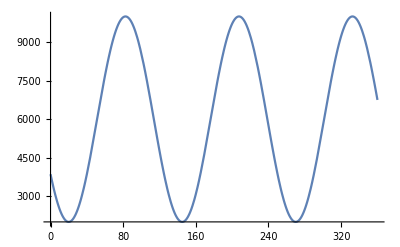

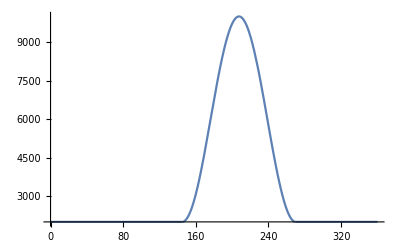

```mathematica
(*Typically the values would be FirstDayOfRain=160 & LastDayOfRain=270. For the PLOS Biol paper use FirstDayOfRain=145.*)
FirstDayOfRain=145 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
LastDayOfRain=270 (* running day in a year of 360 days where each month is exactly 30 days. For example, 180 will be 30 of June *)
phase=LastDayOfRain- FirstDayOfRain; (*This is the length of the rainy season*)
peakShift=phase*3/4-FirstDayOfRain ; (*This shifts the peak of the sin function towards where peak of rainy season should be.*)
K[t_]:=10000*(0.6+0.4*Sin[2π*(t/phase+peakShift/phase)]); (*Division by phase is to match the phase of the sin function to the seasonality; The value of the sin function is -1 to 1 so its multiplication by 0,45 and the addition of 0.55 is to define a minimum (positive) and a maximum value for the number of mosquitos. *) (* Carrying capacity is just a sin function (this is not from the paper). The width (frequency) is matched to the length of the rainy season. the 10000 is just an arbitrary number. Carrying capacity is just for the first 2 stages (denoted "A" in the ODE model below), as their mortality rates depend on carrying capacity *)
f[t_]:=Piecewise[{{K[Mod[t,360]],FirstDayOfRain<Mod[t,360]<LastDayOfRain}},2000];  (*Seasonality in carrying capacity. Here, we mimic the Bongo-District seasonality pattern with a short wet season between Jun-Oct (days 180-300) and a prolonged
dry season between Nov-May (days 0-179 and 301-360). In the rainy season, calculate K. Otherwise set to a baseline of 100 *)
Plot[K[t],{t,0,360}]
Plot[f[t],{t,0,360}]
```

## Mortality rates

### Non - adult mortality rates

```mathematica
(* MuE and MuL are the daily mortality of eggs+early larvae and of late larva stages, respectively. 
Both are density-dependent on the number of early and late larva stages, calculated as (A+L)/f, where f is the environmental carrying capacity at time t; 
\mu_E^0 and \mu_L^0 are assumed to be 0.035 and γ = 13.25. These values are taken from Table 1.
The equations are Eq. 7 in the paper.
*)
```

```mathematica
MuE[t_]:=0.035*(1+(A[t]+L[t])/f[t]); 
MuL[t_]:=0.035*(1+13.25*(A[t]+L[t])/f[t]);
```

### Adult mortality rates -- this is the definition of the intervention

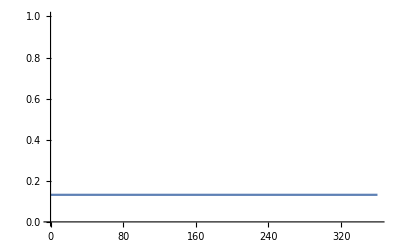

0.8

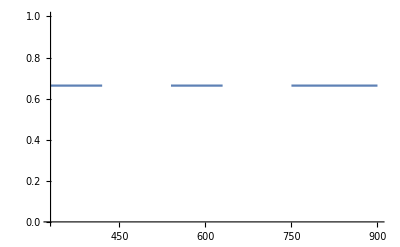

0.9

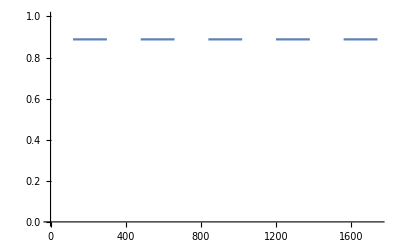

```mathematica
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)

(*MuM is the daily mortality rate of adult mosquitos.The Log turns the w into a rate.*)

(* Example 0: No external mortality rates (no IRS), so c=0 *)
c=0;
TimeMax=360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= {-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,0<t<TimeMax};
Plot[Evaluate[MuM[0,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]

(* Example 1: Our Ghana data. Assume c=0.8 *)
c=0.8
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,330<t<420||540<t<630||750<t<900}},MuM0]; (* The part of 330<t<420||540<t<630||750<t<900 is the IRS scheme of our Ghana data. *)
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,1000},PlotRange->{0,1}]


(* Example 2: IRS of 3 months, May-July, with c=0.9, for 5 years *)
c=0.9
TimeMax=5*360;
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,120<Mod[t,360]<300}},MuM0];
Plot[Evaluate[MuM[c,0.92,0.97,0.207,0.86,t]],{t,0,TimeMax},PlotRange->{0,1}]
(* Plot the mortality rates *)
```

## Mosquito population dynamics without IRS (only seasonality)

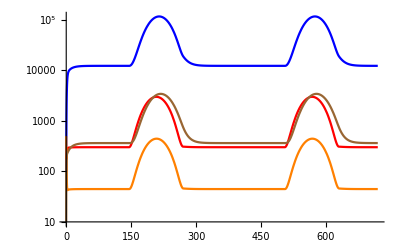

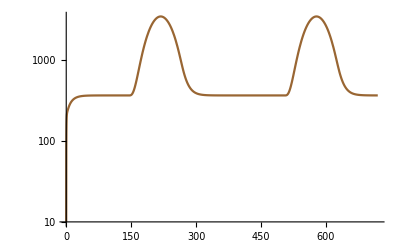

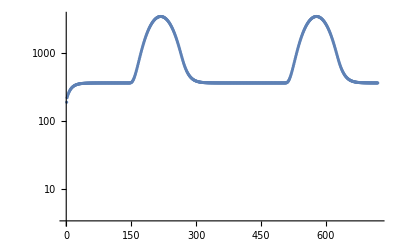

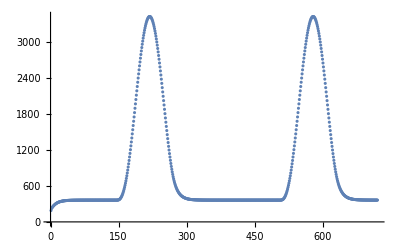

```mathematica
(* When there is no IRS then the mortality rate of adults is just the basline MuM0. This goes in the calculation of M'[t] *)

TimeMax=720;
β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM0*M[t], (* Adult mosquitos, half of them are female *)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown, Purple}] (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}] (* Plot abundance of adults *)
MosquitoNoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];

data=Transpose@{Range[0,TimeMax],Flatten[MosquitoNoIRS,2]};
data=Delete[data,1];
ListLogPlot[data, PlotRange->{0,Max[data]+1}]
ListPlot[data, PlotRange->{0,Max[data]+1}]
(*Export["~/Documents/malaria_interventions/mosquito_population_plosbiol_5.csv",data[[361;;720]]];*)
```

```mathematica
data[[361;;720]]
```

{{1,189.786},{2,221.458},{3,233.813},{4,244.237},{5,254.096},{6,263.328},{7,271.873},{8,279.736},{9,286.95},{10,293.559},{11,299.608},{12,305.143},{13,310.206},{14,314.835},{15,319.067},{16,322.935},{17,326.47},{18,329.7},{19,332.651},{20,335.347},{21,337.81},{22,340.06},{23,342.114},{24,343.991},{25,345.705},{26,347.27},{27,348.699},{28,350.003},{29,351.195},{30,352.283},{31,353.276},{32,354.183},{33,355.01},{34,355.766},{35,356.456},{36,357.086},{37,357.661},{38,358.186},{39,358.665},{40,359.102},{41,359.502},{42,359.866},{43,360.199},{44,360.503},{45,360.78},{46,361.033},{47,361.264},{48,361.475},{49,361.667},{50,361.843},{51,362.003},{52,362.15},{53,362.283},{54,362.405},{55,362.516},{56,362.618},{57,362.711},{58,362.795},{59,362.873},{60,362.943},{61,363.008},{62,363.066},{63,363.12},{64,363.169},{65,363.214},{66,363.254},{67,363.292},{68,363.326},{69,363.357},{70,363.385},{71,363.411},{72,363.434},{73,363.456},{74,363.475},{75,363.493},{76,363.51},{77,363.525},{78,363.538},{79,363.551},{80,363.562},{81,363.572},{82,363.582},{83,363.591},{84,363.598},{85,363.606},{86,363.612},{87,363.618},{88,363.624},{89,363.629},{90,363.633},{91,363.637},{92,363.641},{93,363.645},{94,363.648},{95,363.651},{96,363.653},{97,363.656},{98,363.658},{99,363.66},{100,363.662},{101,363.663},{102,363.665},{103,363.666},{104,363.668},{105,363.669},{106,363.67},{107,363.671},{108,363.672},{109,363.672},{110,363.673},{111,363.674},{112,363.674},{113,363.675},{114,363.676},{115,363.676},{116,363.676},{117,363.677},{118,363.677},{119,363.678},{120,363.678},{121,363.678},{122,363.678},{123,363.679},{124,363.679},{125,363.679},{126,363.679},{127,363.679},{128,363.679},{129,363.68},{130,363.68},{131,363.68},{132,363.68},{133,363.68},{134,363.68},{135,363.68},{136,363.68},{137,363.68},{138,363.68},{139,363.68},{140,363.68},{141,363.68},{142,363.68},{143,363.681},{144,363.681},{145,363.681},{146,363.693},{147,363.866},{148,364.494},{149,365.883},{150,368.315},{151,372.043},{152,377.291},{153,384.259},{154,393.121},{155,404.029},{156,417.115},{157,432.49},{158,450.252},{159,470.479},{160,493.238},{161,518.579},{162,546.542},{163,577.151},{164,610.419},{165,646.347},{166,684.922},{167,726.12},{168,769.905},{169,816.23},{170,865.035},{171,916.25},{172,969.793},{173,1025.57},{174,1083.49},{175,1143.42},{176,1205.26},{177,1268.88},{178,1334.13},{179,1400.89},{180,1468.98},{181,1538.27},{182,1608.6},{183,1679.79},{184,1751.67},{185,1824.09},{186,1896.85},{187,1969.79},{188,2042.73},{189,2115.49},{190,2187.88},{191,2259.73},{192,2330.86},{193,2401.1},{194,2470.26},{195,2538.17},{196,2604.67},{197,2669.59},{198,2732.76},{199,2794.03},{200,2853.24},{201,2910.23},{202,2964.88},{203,3017.03},{204,3066.56},{205,3113.34},{206,3157.26},{207,3198.19},{208,3236.05},{209,3270.73},{210,3302.14},{211,3330.21},{212,3354.86},{213,3376.04},{214,3393.68},{215,3407.75},{216,3418.2},{217,3425.01},{218,3428.17},{219,3427.67},{220,3423.5},{221,3415.68},{222,3404.23},{223,3389.18},{224,3370.56},{225,3348.42},{226,3322.82},{227,3293.83},{228,3261.51},{229,3225.95},{230,3187.25},{231,3145.49},{232,3100.78},{233,3053.25},{234,3003.},{235,2950.17},{236,2894.89},{237,2837.3},{238,2777.56},{239,2715.8},{240,2652.19},{241,2586.89},{242,2520.06},{243,2451.88},{244,2382.53},{245,2312.17},{246,2240.99},{247,2169.16},{248,2096.88},{249,2024.33},{250,1951.69},{251,1879.16},{252,1806.9},{253,1735.13},{254,1664.},{255,1593.72},{256,1524.46},{257,1456.4},{258,1389.72},{259,1324.58},{260,1261.17},{261,1199.64},{262,1140.16},{263,1082.87},{264,1027.94},{265,975.501},{266,925.692},{267,878.642},{268,834.474},{269,793.299},{270,755.223},{271,720.323},{272,688.517},{273,659.569},{274,633.227},{275,609.254},{276,587.435},{277,567.574},{278,549.494},{279,533.032},{280,518.043},{281,504.392},{282,491.958},{283,480.633},{284,470.315},{285,460.915},{286,452.349},{287,444.543},{288,437.429},{289,430.944},{290,425.033},{291,419.644},{292,414.731},{293,410.251},{294,406.167},{295,402.442},{296,399.044},{297,395.946},{298,393.12},{299,390.542},{300,388.191},{301,386.046},{302,384.089},{303,382.304},{304,380.675},{305,379.189},{306,377.834},{307,376.596},{308,375.468},{309,374.438},{310,373.498},{311,372.64},{312,371.857},{313,371.143},{314,370.491},{315,369.897},{316,369.354},{317,368.858},{318,368.406},{319,367.994},{320,367.617},{321,367.273},{322,366.96},{323,366.674},{324,366.412},{325,366.174},{326,365.956},{327,365.758},{328,365.576},{329,365.411},{330,365.26},{331,365.122},{332,364.996},{333,364.882},{334,364.777},{335,364.681},{336,364.594},{337,364.514},{338,364.441},{339,364.375},{340,364.314},{341,364.259},{342,364.209},{343,364.163},{344,364.121},{345,364.082},{346,364.047},{347,364.015},{348,363.986},{349,363.959},{350,363.935},{351,363.913},{352,363.893},{353,363.874},{354,363.857},{355,363.842},{356,363.828},{357,363.815},{358,363.803},{359,363.793},{360,363.783}}

## Mosquito population dynamics with IRS

```mathematica
(* Need to set the IRS scheme, so change these next three lines as necessary, see the examples above *)
w[c_,Q_,ϕ_,r_,ψ_]:=1-Q*c*ϕ*(1-(1-r)(1-ψ)); (* A function indicating how IRS cahnges the adult mortatlity rate. c is coverge and it is the only parameter here we should change. Parameters and their values are taken from Table S3 in the supplementary information *)
FirstDay=120;
LastDay=300;
TimeMax=2*360;
c=0.9;

generateIRS[FirstDay_, LastDay_, TimeMax_, coverage_] := {

filename="~/Documents/malaria_interventions_data/IRS_"<>ToString[FirstDay]<>"_"<>ToString[LastDay]<>"_"<>ToString[coverage]<>"_"<>ToString[TimeMax]<>".csv";
MuM [c_,Q_,ϕ_,r_,ψ_,t_]:= Piecewise[{{-Log[0.91*w[c,Q,ϕ,r,ψ]*0.74/1-Q *c* ϕ* r*0.74]/3,FirstDay<Mod[t,360]<LastDay}},MuM0];

β=21.19; (* Average number of eggs laid per day; value from Table 1*)
de=6.64; (* length of developmental period of eggs+early larvae in days; the reciprocal of dE is the rate of progression to the next stage; value from Table 1*)
dl=3.72; (* length of developmental period of late larvae in days; Instars that survive development will become pupae at a rate given by the reciprocal of dL; value from Table 1*)
     dp=0.64; (*  length of developmental period of pupae, in days; Value from Table 1 *)
MuM0=0.096; (* Daily mortality rate of adult mosquitos; value from Table 1*)
MuP=0.25; (* The pupae daily mortality rate; value ftom Table 1*)
system = {
A'[t] == β* M[t]-A[t]/de-MuE [t]A[t], (*Eggs and early larvae stages*)
L'[t]==A[t]/de-L[t]/dl-MuL[t]*L[t],(*late larvae stages*)
P'[t]==L[t]/dl-P[t]/dp-MuP*P[t], (*Pupae*)
M'[t]==0.5*P[t]/dp-MuM[coverage,0.92,0.97,0.207,0.86,t]*M[t], (*Adult mosquitos, half of them are female*)
(* Initial conditions *)
M[0]==10,
A[0]==100,
P[0]==500,
L[0]==200
};
sol = NDSolve[system,{A[t],L[t],P[t],M[t]},{t,0,TimeMax}];
LogPlot[Evaluate[{A[t],L[t],P[t],M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Blue,Red,Orange,Brown}]; (* Plot abundance of all stages *)
LogPlot[Evaluate[{M[t]}/.sol],{t,0,TimeMax}, PlotStyle->{Brown}]; (* Plot abundance of adults *)
MosquitoIRS=Table[Evaluate[{M[t]}/.sol],{t,0,TimeMax}];(* Obtain mosquito abundance with intervention*)

data=Transpose@{Range[0,TimeMax],Flatten[MosquitoIRS,2]};
data=Delete[data,1];
Export[filename,data];
data
}
```

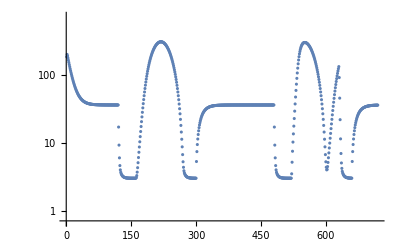

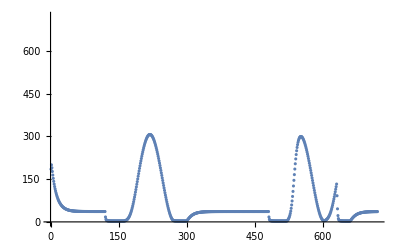

```mathematica
d=generateIRS[120,300,2*360,0.9];
ListLogPlot[d, PlotRange->{0,Max[d]+1}]
ListPlot[d, PlotRange->{0,Max[d]+1}]
```

```mathematica
LengthRange=360*Range[5,20,5];
CoverageRange=Range[0.8,1,0.05];
Table[generateIRS[120,300,a,b],{a,LengthRange},{b,CoverageRange}];
```

```mathematica
5
```